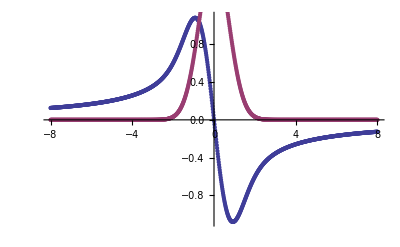

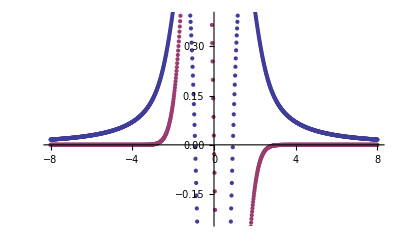

```mathematica
Z[re_,im_]:= I Sqrt[Pi] Exp[-(re+ I im)^2] Erfc[-I (re+I im)];
Zp[re_,im_]:=-2 (1+(re+I im) Z[re,im]);
zReMin=-8;zReMax=8;nPtsRe=1000;
zRe=N[Table[re,{re,zReMin,zReMax,(zReMax-zReMin)/(nPtsRe-1)}]];
ZData=Z[zRe,0];
ZPData=Zp[zRe,0];
ListPlot[{Re[ZData],Im[ZData]},DataRange->{zReMin,zReMax}]
ListPlot[{Re[ZPData],Im[ZPData]},DataRange->{zReMin,zReMax}]
Export["zFunction.nc",{zRe,Re[ZData],Im[ZData],Re[ZPData],Im[ZPData]},{"Datasets",{"arg_re","Z_re","Z_im","Zp_re","Zp_im"}}];
```